```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/yunqiguo/Document/CS249_2/project/249-Sun/src

```mathematica
purity[c_,w_]:=Module[{inter},
inter=Table[Length@Intersection[c[[i]],w[[j]]],{i,Length@c},{j,Length@w}];
Return@N[(Total@(Max/@inter))/(Total@(Length/@c))]
]
```

```mathematica
<<../data/edges.mx
```

```mathematica
<<../data/top5.mx
```

```mathematica
g=Graph[edges];
```

```mathematica
communities=FindGraphPartition[g,500];
```

```mathematica
distance=GraphDistanceMatrix[g];
```

```mathematica
vDic = Association@Table[#[[i]]->i,{i,Length@#}]&@VertexList[g];
```

```mathematica
vDic[[1;;10]]
```

<|61→1,45116→2,48574→3,55007→4,57571→5,63075→6,72070→7,88279→8,93348→9,116767→10|>

```mathematica
communityDistanceMatrix=Table[N@Mean@Flatten@distance[[vDic/@communities[[i]],vDic/@communities[[j]]]],{i,500},{j,500}];
```

```mathematica
g2=WeightedAdjacencyGraph[1/communityDistanceMatrix];
```

```mathematica
communities4=FindGraphCommunities[g2,Method->"Spectral"];
```

```mathematica
Length/@communities4
```

{107,93,93,65,32,29,18,16,14,12,5,5,3,2,2,2,1,1}

```mathematica
distance2=GraphDistanceMatrix[g2];
```

```mathematica
...
```

```mathematica
purity[Flatten[communities[[#]]]&/@communities4,top5]
```

0.688972

```mathematica
Dynamic[bd]
```

```mathematica
result={};
For[bd=4,bd<8,bd+=0.1,
bound=bd;
filter[t_]:=If[t<bound,1,0];
adjancyMaptrix=Map[filter,communityDistanceMatrix,{2}];
g3=AdjacencyGraph[adjancyMaptrix];
communities2=FindGraphPartition[g3,5];
communities3=Flatten[communities[[#]]]&/@communities2;
AppendTo[result,{bd,purity[communities3,top5]}];
]
```

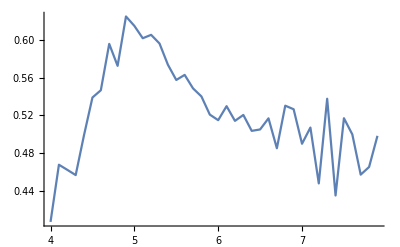

```mathematica
ListPlot[result,Joined->True]
```

Baseline

```mathematica
communities0=FindGraphPartition[g,5];
```

```mathematica
(*communities0=FindGraphCommunities[g];*)
```

```mathematica
purity[communities0,top5]
```

0.682072

use spectral method

```mathematica
adjancy=1/communityDistanceMatrix;
Table[adjancy[[i,i]]=0,{i,Length@adjancy}];
k=DiagonalMatrix@(Total/@adjancy);
m=Total@Flatten[k];
```